```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
ResourceFunction["MaTeXInstall"][];
<<MaTeX`
texout={Frame->True,ImageSize->410,BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->12}};
```

```mathematica
F[a_,w_,v_]:=ParabolicCylinderD[v,w] ParabolicCylinderD[v+1,-w]+ParabolicCylinderD[v,-w] ParabolicCylinderD[v+1,w]+a ParabolicCylinderD[v,w] ParabolicCylinderD[v,-w]
```

```mathematica
cfce[x_] := {
Piecewise[{ {1, x>0.5}, {0.6,x<0.5} , {0.6, x==0}}],
Piecewise[{ {0.6, x>0.5}, {0.6, x<0.5}, {0.6, x==0} }],
Piecewise[{ {0.6, x>0.5}, {1, x<0.5}, {0.6, x==0} }]
};
cfceBlend[x_] := Blend[RGBColor[cfce[#]] &/@ (Range[100]/100), x];
```

```mathematica
plot[a_]:=Show[
DensityPlot[2 LogisticSigmoid[ F[a,w/Sqrt[2],(v-1)/2]]-1,{w,-10,10},{v,-1,9.01},
ColorFunction->cfceBlend,
ClippingStyle->Automatic,
PlotLegends->None,
Evaluate@texout,
PlotLabel->MaTeX /@ {"\\alpha \\, \\sqrt{2b} = "<>ToString[a]},
FrameLabel->MaTeX/@{"p / \\sqrt{b}","\\epsilon / b"},
PerformanceGoal->"Quality"
],
ContourPlot[
F[a,w/Sqrt[2],(v-1)/2]==0, 
{w,-10,10},{v,-1,9.01},
ColorFunction->Function[x,{0,0.5,0}]
]
];
```

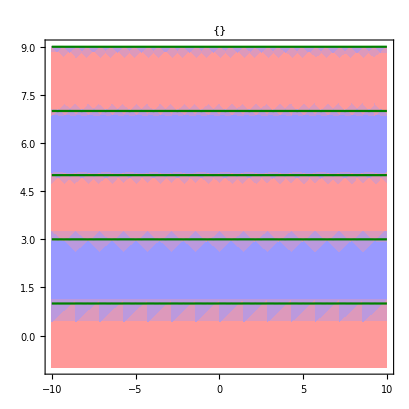

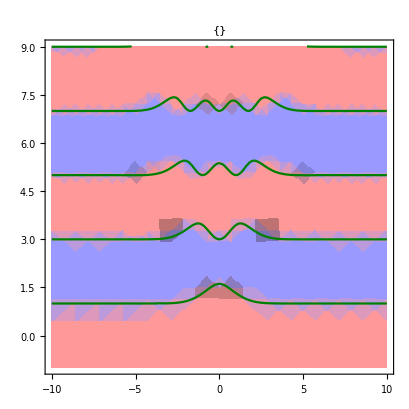

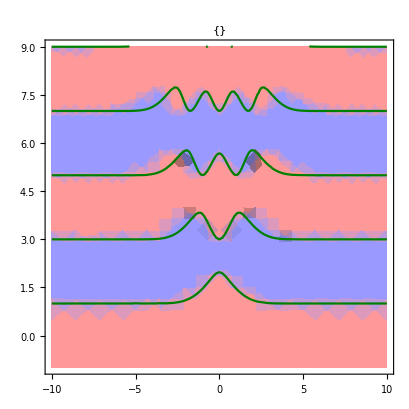

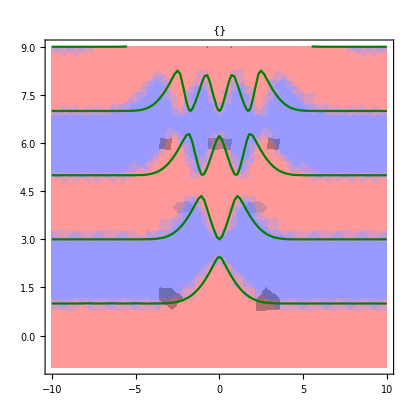

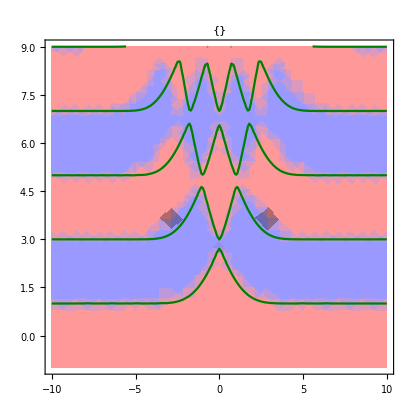

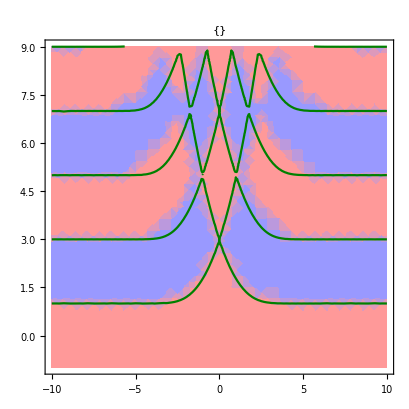

```mathematica
p = plot[0]
Export["dirac0.pdf",p,ImageResolution->600];

p = plot[1]
Export["dirac1.pdf",p,ImageResolution->600];

p = plot[2]
Export["dirac2.pdf",p,ImageResolution->600];

p = plot[5]
Export["dirac5.pdf",p,ImageResolution->600];

p = plot[10]
Export["dirac10.pdf",p,ImageResolution->600];

p = plot[100]
Export["dirac100.pdf", p, ImageResolution->600];
```

```mathematica
plotContour[a_] := ContourPlot[
F[a,w/Sqrt[2],(v-1)/2]==0, 
{w,-15,15},{v,-3,8.99},
ColorFunction->Function[x,{0,0,0}],
Evaluate@texout,
PlotLabel->MaTeX /@ {"\\alpha \\, \\sqrt{2b} = "<>ToString[a]},
FrameLabel->MaTeX/@{"p / \\sqrt{b}","\\epsilon / b"},
PerformanceGoal->"Quality"
];
```

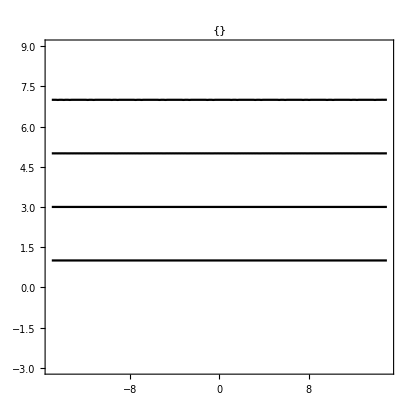

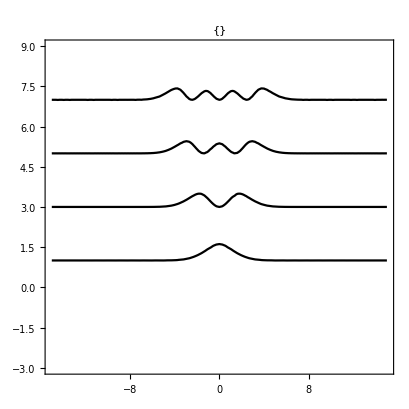

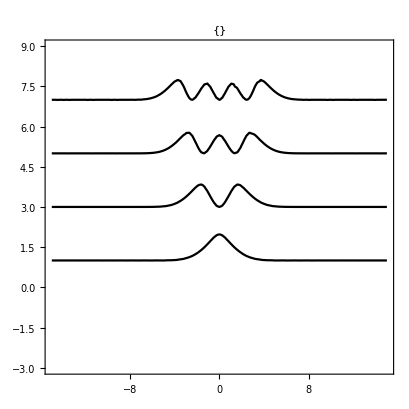

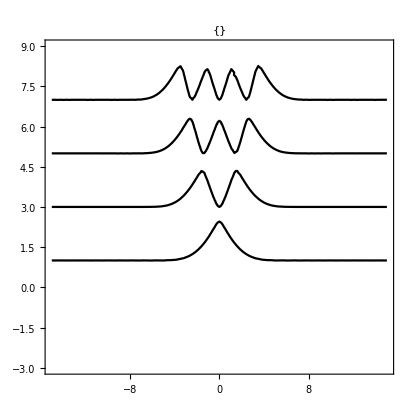

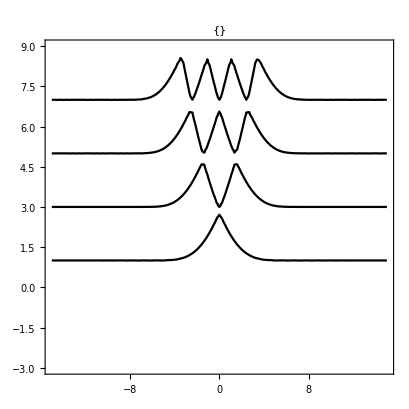

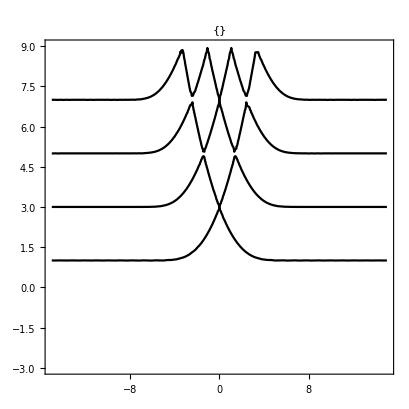

```mathematica
p = plotContour[0]
Export["dirac0.pdf",p,ImageResolution->600];

p = plotContour[1]
Export["dirac1.pdf",p,ImageResolution->600];

p = plotContour[2]
Export["dirac2.pdf",p,ImageResolution->600];

p = plotContour[5]
Export["dirac5.pdf",p,ImageResolution->600];

p = plotContour[10]
Export["dirac10.pdf",p,ImageResolution->600];

p = plotContour[100]
Export["dirac100.pdf",p,ImageResolution->600];
```

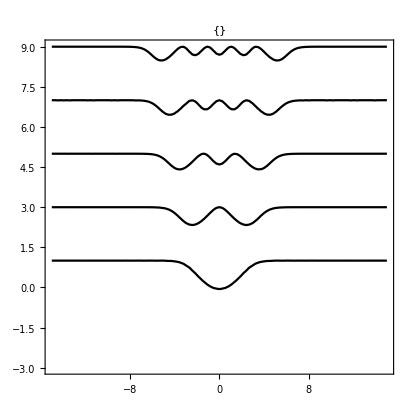

```mathematica
p = plotContour[-1]
Export["dirac-1.pdf",p,ImageResolution->600];


p = plotContour[-2]
Export["dirac-2.pdf",p,ImageResolution->600];


p = plotContour[-5]
Export["dirac-5.pdf",p,ImageResolution->600];


p = plotContour[-10]
Export["dirac-10.pdf",p,ImageResolution->600];


p = plotContour[-100]
Export["dirac-100.pdf",p,ImageResolution->600];
```

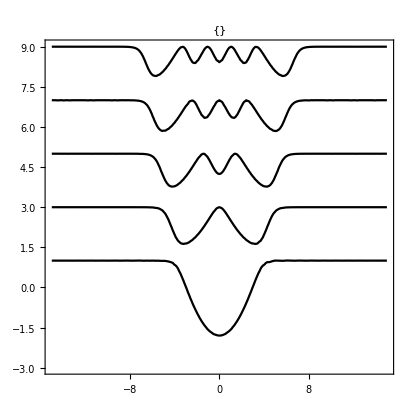

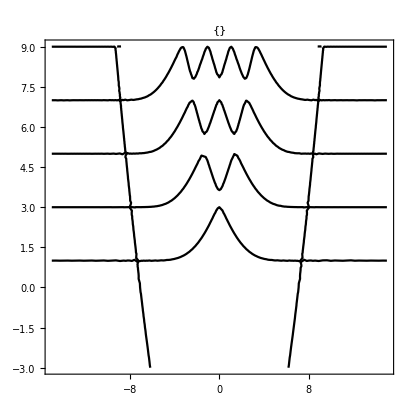

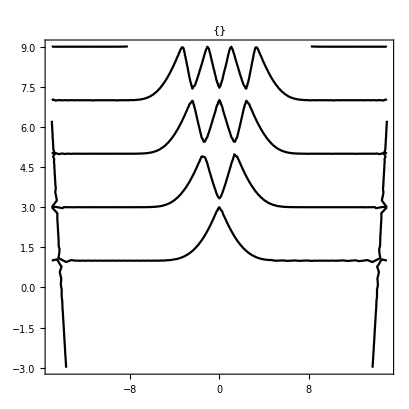

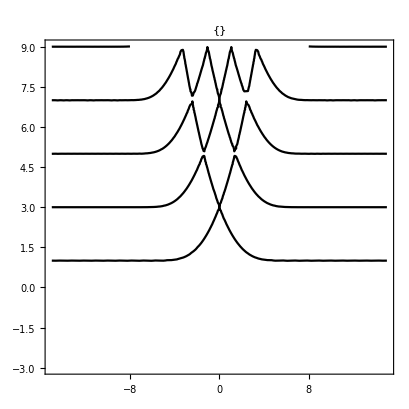

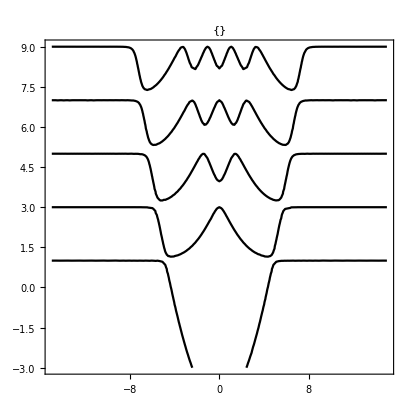

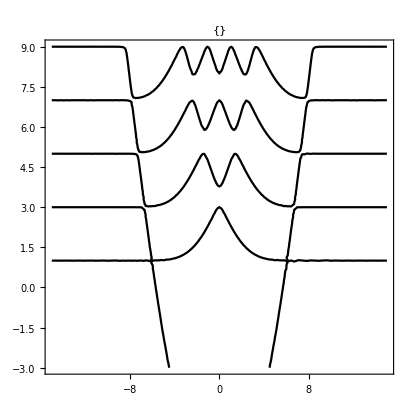

```mathematica
p = plotContour[-3]
Export["dirac-3.pdf",p,ImageResolution->600];

p = plotContour[-4]
Export["dirac-4.pdf",p,ImageResolution->600];
```

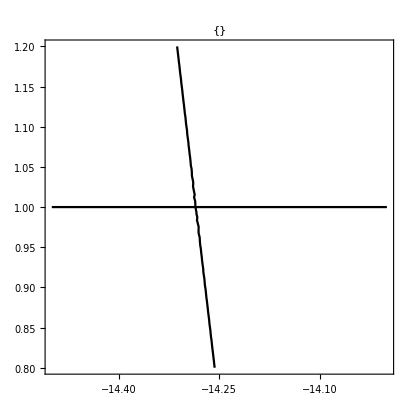

```mathematica
ContourPlot[
F[-10,w/Sqrt[2],(v-1)/2]==0, 
{w,-14.5,-14},{v,0.8,1.2},
ColorFunction->Function[x,{0,0,0}],
Evaluate@texout,
PlotLabel->MaTeX /@ {"\\alpha \\, \\sqrt{2b} = "<>ToString[a]},
FrameLabel->MaTeX/@{"p / \\sqrt{b}","\\epsilon / b"},
PerformanceGoal->"Quality"
]
```

```mathematica
najdiMinimum[a_,k_] := Minimize[
{v, F[a,w/Sqrt[2],(v-1)/2]== 0,v≤k+1,v>k},
{w,v}
][[1]]
Plot[N[najdiMinimum[-a,1],1][[1]], {a,0, 5}, MaxRecursion->1,PerformanceGoal->"Speed", PlotPoints->5]
```

$Aborted

```mathematica
N[Minimize[
{v-1, F[#,w/Sqrt[2],(v-1)/2]== 0, v≤2, v>1},
{w,v}
],15][[1]] & /@ {-1, -2}
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
N[Minimize[
{v, F[-3,w/Sqrt[2],(v-1)/2]== 0,v≤1+1,v>1},
{w,v}
],5]
```

{1.0003,{w→6.312,v→1.0003}}

```mathematica
nM[a_, k_, n_, ε_] := N[FindMinimum[
{2(ν-k), F[a, w/Sqrt[2],ν]==0, ν≤k+1, ν>k+ε, w>-10, w<10},
{{ν,k+1},{w,-8}}
],n]
```

```mathematica
nM[-1,2,5, 10^-5]
```

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

{0.00002,{ν→2.00001,w→9.53781}}

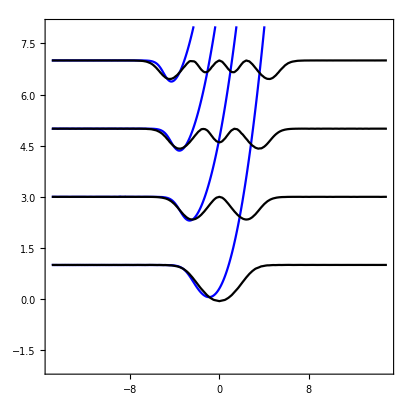

```mathematica
FRobin[a_, p_, ε_] := (a + p) ParabolicCylinderD[(ε-1)/2,p Sqrt[2]] -Sqrt[2] ParabolicCylinderD[(ε+1)/2,p Sqrt[2]];

p = Show[
ContourPlot[
 FRobin[0.5,0.6p,ε]==0,
{p,-15,15},{ε,-2,8},
ColorFunction->Function[x,{0,0,1}],
Evaluate@texout,
FrameLabel->MaTeX/@{"p / \\sqrt{b}","\\epsilon / b"},
PerformanceGoal->"Quality",
WorkingPrecision->200,
MaxRecursion -> 3
],
ContourPlot[
F[-1,w/Sqrt[2],(v-1)/2]==0, 
{w,-15,15},{v,-3,8},
ColorFunction->Function[x,{0,0,0}],
Evaluate@texout,
FrameLabel->MaTeX/@{"p / \\sqrt{b}","\\epsilon / b"},
PerformanceGoal->"Quality"
]
]

Export["dirac-robin.pdf",p,ImageResolution->600];
```

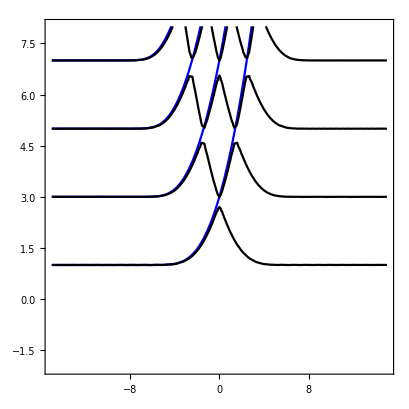

```mathematica
p = Show[
ContourPlot[
 ParabolicCylinderD[(ε-1)/2,p / Sqrt[2]]==0,
{p,-15,15},{ε,-2,8},
ColorFunction->Function[x,{0,0,1}],
Evaluate@texout,
FrameLabel->MaTeX/@{"p / \\sqrt{b}","\\epsilon / b"},
PerformanceGoal->"Quality",
WorkingPrecision->200,
MaxRecursion -> 3
],
ContourPlot[
F[10,w/Sqrt[2],(v-1)/2]==0, 
{w,-15,15},{v,-3,8},
ColorFunction->Function[x,{0,0,0}],
Evaluate@texout,
FrameLabel->MaTeX/@{"p / \\sqrt{b}","\\epsilon / b"},
PerformanceGoal->"Quality"
]
]

Export["dirac-dirichlet.pdf",p,ImageResolution->600];
```